```mathematica
table1=({{14, 165, 2}, {14.2, 166, 2}, {14.4, 166, 2}, {14.6, 167, 2}, {14.7, 167, 10}, {14.8, 167, 23}, {14.9, 168, 38}, {15, 168, 54}, {15.1, 168, 72}, {15.2, 169, 95}, {15.3, 169, 116}, {15.4, 169, 131}, {15.5, 170, 152}, {15.6, 170, 170}, {15.7, 170, 194}, {15.8, 171, 218}, {15.9, 171, 254}, {16, 171, 284}, {16.1, 172, 320}, {16.2, 172, 320}, {16.3, 172, 386}, {16.4, 173, 425}, {16.5, 173, 464}, {16.6, 173, 490}, {16.7, 174, 538}, {16.8, 174, 599}, {16.9, 175, 642}, {17, 175, 690}, {17.1, 176, 736}, {17.2, 176, 790}, {17.3, 176, 835}, {17.4, 177, 883}});
```

```mathematica
For[i=1,i≤ Length[table1],i++,
table1[[i,1]]=Quantity[table1[[i,1]],"Amperes"];
table1[[i,2]]=Quantity[table1[[i,2]],"Millivolts"];
table1[[i,3]]=Quantity[table1[[i,3]],"Milliwatts"];
]
```

```mathematica
table1=Transpose[Append[Transpose[table1],UnitConvert[table1[[All,1]]*table1[[All,2]],"Watts"]]];
```

```mathematica
table2=({{14.4, 167, 2}, {14.5, 167, 14}, {14.6, 168, 35}, {14.7, 168, 51}, {14.8, 168, 69}, {14.9, 169, 85}, {15, 169, 102}, {15.1, 169, 121}, {15.2, 170, 140}, {15.3, 170, 161}, {15.4, 170, 182}, {15.5, 171, 203}, {15.6, 171, 232}, {15.7, 171, 257}, {15.8, 172, 283}, {15.9, 172, 297}, {16, 172, 325}, {16.1, 172, 357}, {16.2, 173, 397}, {16.3, 173, 432}, {16.4, 174, 470}, {16.5, 174, 511}, {16.6, 174, 531}, {16.7, 174, 562}, {16.8, 175, 602}, {16.9, 175, 641}, {17, 175, 686}, {17.1, 176, 727}, {17.2, 176, 772}, {17.3, 176, 810}, {17.4, 177, 854}});
```

```mathematica
For[i=1,i≤ Length[table2],i++,
table2[[i,1]]=Quantity[table2[[i,1]],"Amperes"];
table2[[i,2]]=Quantity[table2[[i,2]],"Millivolts"];
table2[[i,3]]=Quantity[table2[[i,3]],"Milliwatts"];
]
```

```mathematica
table2=Transpose[Append[Transpose[table2],UnitConvert[table2[[All,1]]*table2[[All,2]],"Watts"]]];
```

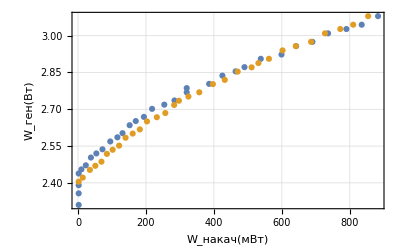

```mathematica
ListPlot[{table1[[All,3;;4]],table2[[All,3;;4]]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"W_(:043d:0430:043a:0430:0447)(мВт)","W_(:0433:0435:043d)(Вт)"}]
```